# Hands-On Start to Mathematica

## This is a basic start to Mathematica, Bhawin Dhital, September 14, 2020, Jefferson Lab

## Notebook: Basic Algebra

```mathematica
2+2
```

4

```mathematica
1+2+3
```

6

```mathematica
%+4
```

10

After you perform a calculation, the Suggestions Bar will provide options for further computation:

Standard symbols work for mathematical operations:
(Use a space or * for multiplication, not the “x” character.)

```mathematica
5+2*3-7.5
```

3.5

```mathematica
((5-3)^(1+2))/4
```

2

There are many built-in function. For example, Greatest Common Divisor (GCD) can be calculated as:

```mathematica
GCD[12,15]
```

3

Fractions and Decimals

```mathematica
1/4+1/3
```

7/12

(Use CTRL+ / to enter fractions.)

```mathematica
1/2+ 1/2
```

1

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)

```mathematica
.25+1/3
```

0.583333

To get a numerical estimates of result:

```mathematica
N[1/4+1/7]
```

0.392857

To specify the accuracy to which your answer is displayed

```mathematica
N[1/4+1/7,10]
```

0.3928571429

To express in scientific form:

```mathematica
ScientificForm[0.00123]
```

1.23×10^-3

ScientificForm is applied automatically when appropriate, for example:

```mathematica
N[100!]
```

9.33262×10^157

Variables and functions: variables start with letters and can also contain numbers

```mathematica
a1/2
```

a1/2

A space between two variables or numbers indicates multiplication: for example a b means a*b

```mathematica
a b + 5 x x
```

a b+5 x^2

```mathematica
ab+5xx
```

ab+5 xx

Use /. and → to make substitutions in an expression, for example if you want to replace x by 2 in this example then:

```mathematica
1+2 x/.x->2
```

5

You can assign a value using a symbol. For example:

```mathematica
x=2
```

2

```mathematica
1+2 x
```

5

You can define a function yourself, for example:

```mathematica
f[x_]=1 + 3 x
```

7

```mathematica
x=5
```

5

```mathematica
f[x_]=1+3 x
```

```mathematica
16
```

```mathematica
Clear[x]
```

Use ctrl + 6 for the exponent.

Algebra and properties: we can factor or expand algebraic expressions:

```mathematica
Factor[x^2+2 x + 1]
```

36

```mathematica
2+2==4
```

True

```mathematica
1+z==15
```

1+z==15

Here, == is used to represent an equation:

To solve an inequality:

```mathematica
Solve[x^2+5 x-6==0,x]
```

{{x→-6},{x→1}}

For approximate results, use NSolve

```mathematica
NSolve[7 x^2+3 x-5==0,x]
```

{{x→-1.08618},{x→0.657611}}

You can solve the system of equations:

```mathematica
Solve[{x^2+5==y, 7 x - 5 ==y},{x,y}]
```

{{x→2,y→9},{x→5,y→30}}

To find the root of an equation: just use Roots function

```mathematica
Roots[x^2+3x-4==0,x]
```

x==-4||x==1

If a polynomial is not easily factorable, approximate results may be more useful

```mathematica
NRoots[360+234 x-1051 x^2+11 x^3+304 x^4-20 x^5==0,x]
```

x==-1.79025||x==-0.498678||x==0.797819||x==1.68398||x==15.0071

The Reduce command reduces a set of inequalities into a simple form: Type <= for less than and equal to

```mathematica
Reduce[{0<x<2,1≤x≤4},x]
```

1≤x<2

NumberLinePlot is a handy way to visualize these results

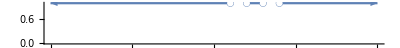

```mathematica
NumberLinePlot[x<1||2<x<3||x>4,{x,-10,10}]
```

```mathematica
Solve[a x^2 + b x +c==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Solve simultaneous equations:

```mathematica
Solve[{3 x + 2 y == 15, 3 x -3 y == 12}] // N
```

{{x→4.6,y→0.6}}

```mathematica
Solve[{3 x + 2 y == 15, 3 x -3 y == 12},{x,y}] // N
```

{{x→4.6,y→0.6}}

```mathematica
Solve[{3 a x + 2 y ==15, 3 x - 3 b y ==12},{x,y}] // N
```

{{x→-(1. (-8.-15. b))/(2.+3. a b),y→-(3. (-5.+4. a))/(2.+3. a b)}}

```mathematica
Solve[{3 a x + 2 y ==15, 3 x - 3 b y ==12},{x,y}]
```

{{x→-(-8-15 b)/(2+3 a b),y→-(3 (-5+4 a))/(2+3 a b)}}